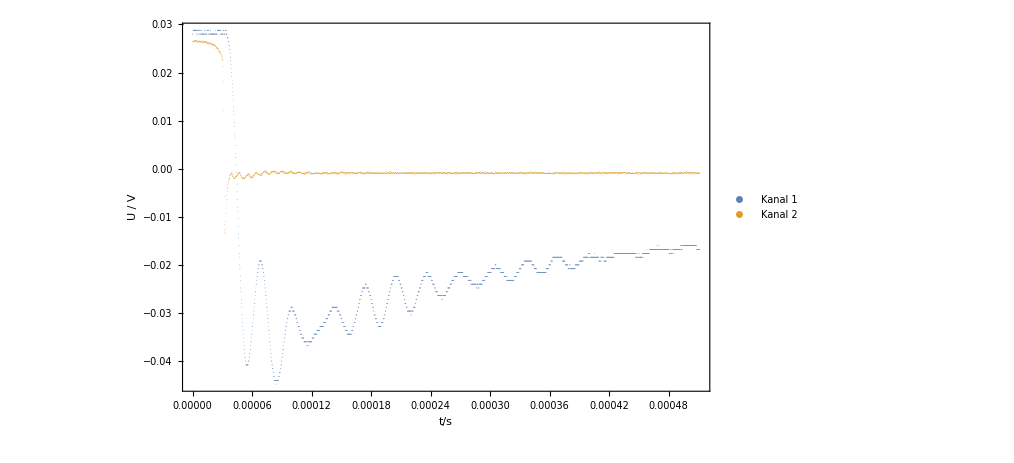

```mathematica
path = "./02-63.7mA-100mA.tab";
ch1zoom = 1;
ch2zoom = 1;
SetDirectory[NotebookDirectory[]];
data = Drop[Import[path], 1];
ch1 = Transpose[{data[[All,1]],data[[All,2]]*ch1zoom}];
ch2 = Transpose[{data[[All,1]],data[[All,3]]*ch2zoom}];
ListPlot[{ch1, ch2}, PlotRange->All, Frame->True, ImageSize->750, PlotStyle->{PointSize[0.0001]}, PlotLegends->{"Kanal 1"<>If[ch1zoom ≠ 1, " x "<>ToString[ch1zoom], ""], "Kanal 2"<>If[ch2zoom ≠ 1, " x "<>ToString[ch2zoom], ""]}, FrameLabel->{"t/s", "U / V"}]
```

{8,8,7,6,15,13,9,9,10,7,5,5,5,8,9}

{0,10,20,30,40,50,60,70,75,80,85,87,90,95,100}

{0.,4.38,8.76,13.14,17.52,21.9,26.28,30.66,32.85,35.04,37.23,38.106,39.42,41.61,43.8}

{0.00003966,0.00004471,0.00004564,0.00004548,0.00013968,0.00015341,0.00013171,0.00020211,0.00029325,0.00030403,0.00033,0.0003201,0.0003148,0.00035993,0.00029942}

{4.9575,5.58875,6.52,7.58,9.312,11.8008,14.6344,22.4567,29.325,43.4329,66.,64.02,62.96,44.9913,33.2689}

{{0.,4.9575},{4.38,5.58875},{8.76,6.52},{13.14,7.58},{17.52,9.312},{21.9,11.8008},{26.28,14.6344},{30.66,22.4567},{32.85,29.325},{35.04,43.4329},{37.23,66.},{38.106,64.02},{39.42,62.96},{41.61,44.9913},{43.8,33.2689}}

FittedModel::constr: The property values {"ParameterTable"} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
a | 160. | 2.249×10^6 | 0.0000711427 | 0.999945
b | 40. | 562266. | 0.0000711408 | 0.999945
c | 1.10512 | 15534.3 | 0.0000711407 | 0.999945
d | 0.450142 | 3.48318 | 0.129233 | 0.899506

FittedModel::constr: The property values {"ParameterTableEntries"} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

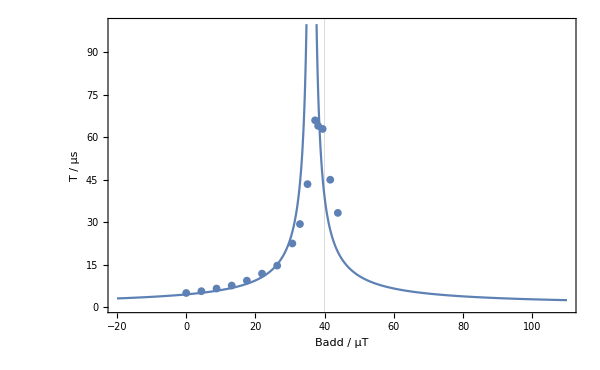

```mathematica
maxpos={{{2.513*^-5,-0.003139},{6.479*^-5,-0.007048}},{{2.697*^-5,-0.003181},{7.168*^-5,-0.008716}},{{2.283*^-5,-0.003121},{6.847*^-5,-0.01225}},{{2.513*^-5,-0.003689},{7.061*^-5,-0.01443}},{{4.842*^-5,-0.00981},{0.0001881,-0.01686}},{{4.199*^-5,-0.004052},{0.0001954,-0.02148}},{{4.689*^-5,-0.0112},{0.0001786,-0.02577}},{{5.979*^-5,-0.01918},{0.0002619,-0.02337}},{{6.975*^-5,-0.02752},{0.000363,-0.03039}},{{8.277*^-5,-0.02019},{0.0003868,-0.01651}},{{0.0001027,-0.01676},{0.0004327,-0.01618}},{{0.0001057,-0.01052},{0.0004258,-0.01403}},{{0.0001011,-0.02195},{0.0004159,-0.02746}},{{8.047*^-5,-0.03641},{0.0004404,-0.03252}},{{6.898*^-5,-0.01933},{0.0003684,-0.01838}}};
maxnum={8,8,7,6,15,13,9,9,10,7,5,5,5,8,9}
current={0,10,20,30,40,50,60,70,75,80,85,87,90,95,100}
B=0.438current
maxdiff=Table[maxpos[[i,2,1]]-maxpos[[i,1,1]],{i,1,Length[maxpos]}]
T=maxdiff/maxnum*10^6
plotdata=Transpose[{B,T}]
fitdata=Drop[plotdata,-0];
Terrors=Drop[maxdiff,-0];
nlm=NonlinearModelFit[fitdata,{Abs[a/(b-c x)]+d,{160<a,37<b,b<40,0.7<c,c<1.3}},{{a,200},{b,39},{c,1.1},{d,1}},x,Weights->1/Terrors^2];
nlm["ParameterTable"]
Show[Plot[Normal[nlm],{x,-20,110},PlotRange->{{-20,110},{0,100}},Frame->True,FrameLabel->{"Badd / µT","T / µs"},GridLines->{{nlm["ParameterTableEntries"][[2,1]]},{}},ImageSize->600],ListPlot[plotdata,PlotMarkers->{Automatic,8}]]
```

```mathematica
Manipulate[Show[Plot[Abs[a/(b-c x)]+d,{x,-20,110},PlotRange->{{-20,110},{0,100}},Frame->True,FrameLabel->{"Badd / µT","T / µs"},GridLines->{{},{}},ImageSize->600],ListPlot[plotdata,PlotMarkers->{Automatic,8}]],{{a,200},100,300},{{b,45},35,60},{{c,1.4},0.8,1.6},{{d,0},-5,5}]
```